```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->None]
```

## Styles and files

```mathematica
runsToGenerate  = {};
```

```mathematica
githubPath= PersistentSymbol["persistentGitHubPath","Local"];
AppendTo[$Path,FileNameJoin[{githubPath,"Packages"}]];
Needs["LatticePhyllotaxis`"];
Needs["DiskStacking`"];
Get["talkStylings.m"]
```

```mathematica
gDrive = PersistentSymbol["persistentGDrive"];
runDirectory = FileNameJoin[{gDrive,"Work\\Textbook\\Stacked coin paper\\Mathematica\\Runs"}];
eSetDirectory = (* post processed runs, no real reason for this to be different from runDirectory *) FileNameJoin[{gDrive,"Work\\Textbook\\Stacked coin paper\\Mathematica\\Esets"}];

draftFigureDirectory = FileNameJoin[{gDrive,"Work\\Textbook\\Stacked coin paper\\DraftFigures"}];


getRunByTag[tag_] := Module[{file},
file = FileNameJoin[{runDirectory,StringJoin[tag,".mx"]}];
If[FileExistsQ[file],Return[Import[file]]];
Print["Can't load ", tag, " from ", file];
Abort[]
];
```

```mathematica
jParastichyColour[n_] := jStyle["ParastichyColour"][n];
jFont[n_] := {FontFamily->  jStyle["FontFamily"],FontSize-> n};
paraColours= <|Red-> jParastichyColour[1],Blue-> jParastichyColour[2]|>;
leftRightColours = <|"Left"-> jParastichyColour[1],"Right"-> jParastichyColour[2]|>;
jBaseStyle= jFont[12];

SetAttributes[jExport,HoldFirst];

jExport[fig_] := Module[{figname},
SetDirectory[draftFigureDirectory];
figname=SymbolName[Unevaluated[fig]];
Export[StringJoin[figname,".jpg"],fig,ImageResolution->300];Export[StringJoin[figname,".pdf"],fig,ImageResolution->300];
ResetDirectory[];
fig
];
```

## tlkNonOpposed Illustrative lattice plot

```mathematica
tlkShowParastichyLines[lattice_,lineColourFunction_]  :=  Module[{ll,llines,paraset,plines,numbers,rise,divergence,glines},
ll =Take[Flatten[ LatticePhyllotaxis`latticeLabel[lattice]],2];
llines = Map[LatticePhyllotaxis`latticeParastichyLines[lattice,#]&,ll];
numbers= KeyValueMap[Style[Text[#1,#2],Background->White]&,KeyTake[lattice["namedLatticePoints"],Range[0,10]]];
rise= Translate[Arrow[{{lattice["namedLatticePoints"][1][[1]],lattice["namedLatticePoints"][0][[2]]},lattice["namedLatticePoints"][1]}],{0.05,0}];
divergence= {Arrow[{lattice["namedLatticePoints"][0],{lattice["namedLatticePoints"][1][[1]],lattice["namedLatticePoints"][0][[2]]}}]};
Graphics[{
{jStyle["CylinderColour"],LatticePhyllotaxis`latticeGraphicsCylinder[lattice]}
,{FaceForm[White],LatticePhyllotaxis`latticeCircles[lattice]/. Circle->Disk},
, {Thick,MapIndexed[{lineColourFunction[First[#2]],#1}&,llines]}
,{PointSize[Small],Point[LatticePhyllotaxis`latticePoints[lattice]]}
},PlotRange->{{-1/2,.6},{-0.05,0.4}}
,BaseStyle->Directive[FontFamily-> jStyle["FontFamily"],FontSize->Scaled[0.03]]
]
];

tlkNonOpposed := Module[{lattice,dh},
dh=LatticePhyllotaxis`latticeDivergenceRiseForNonOpposedTC[{2,5}];
lattice = LatticePhyllotaxis`latticeFromDivergenceRise[dh, {-0.1,0.5}];

tlkShowParastichyLines[lattice,jParastichyColour]
];
tlkOpposed := Module[{lattice,dh},
dh=LatticePhyllotaxis`latticeDivergenceRiseForOpposedTC[{2,5}];
lattice = LatticePhyllotaxis`latticeFromDivergenceRise[dh, {-0.1,0.5}];

tlkShowParastichyLines[lattice,jParastichyColour]
];
tlkONotO := GraphicsRow[{tlkOpposed,tlkNonOpposed}]
```

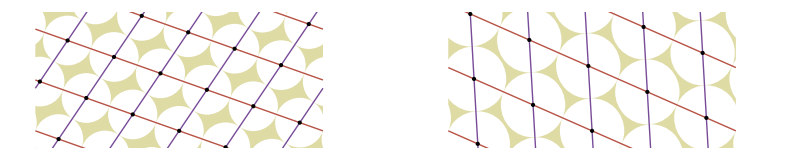

```mathematica
jExport[tlkONotO]
```

## 6 fig : tlkConeTransformation

### Colours

```mathematica
baseColour =  <|
"cone"-> LightGray,
"bract"-> jParastichyColour[3],
"ray"->Darker[Yellow,0.1],
"seed" -> Lighter[ColorData["CoffeeTones"][0.3],0.9],
"inner"->Lighter[ColorData["CoffeeTones"][0.3],0.6]
|>;

polygonColour= baseColour;
polygonBoundaryColour = Map[Black&,baseColour];
polygonBoundaryColour["seed"] = LightGray;

polygonColour3D = baseColour;
(*polygonColour3D["cone"] = Lighter[baseColour["bract"],0.2];
*)
nodeColour = baseColour;
nodeColour["ray"] = White;
nodeColour["seed"] = ColorData["CoffeeTones"][0.3];

cylinderNodeColour = baseColour;
cylinderNodeColour["seed"] = nodeColour["seed"];
cylinderDiskColour = cylinderNodeColour;
cylinderDiskColour["seed"]= baseColour["seed"];
cylinderDiskColour["cone"]= White;
cylinderDiskBoundaryColour= Map[None&,baseColour];
cylinderDiskBoundaryColour["seed"]= LightGray;
cylinderDiskBoundaryColour["cone"]=LightGray;
```

```mathematica
nodeType[{x_,z_}] := 
Which[
z<stemParameters["cone"]["zEnd"],"cone"
,z<stemParameters["bract"]["zEnd"], "bract"
,z<stemParameters["ray"]["zEnd"], "ray"
,z<stemParameters["seed"]["zEnd"],"seed"
,z<∞,"inner"
, True, Missing[]
];
```

### Get run

```mathematica
arena3= <|"runNumber"->1
,"Tag"->"radius-34bis-tlk3"
,"Run"->""
,"radiusFunctionParameters" -> {
<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"->1.7,"zRange"-> 0.1|>
,<|"Type"->"Constant","ApproximateChains"->1|>
,<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"-> 0.9,"zRange"->0.02|>
,<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"-> 0.4/0.9,"zRange"->0.15|>
,<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"-> 0.2/(0.4/0.9),"zRange"->0.05|>
}
,"Noise"->0
,"Lattice"->LatticePhyllotaxis`latticeOrthogonal[{21,34},cylinderLU={-0.01,0.1}]
|>;
(*
runCone  = doOneRun[arena3];

*)
```

```mathematica
retrieveRFunction[savedRun_] := Module[{run,parameters},
parameters=savedRun["Arena"];
run = DiskStacking`runFromLattice[parameters["Lattice"]];
run= readyRunFromParameter[run,parameters] ; 
run["Arena"]["rFunction"]
];
showRFunction[savedRun_] := Module[{getf,ht,ra,getr},
getf= retrieveRFunction[savedRun] ; 
ht=runDisksHeight[savedRun];
 ra=runDisksRadius[savedRun];
 getr = Map[{ht[#],1/ra[#]}&,
Select[diskNumbersInRun[runCone],#>0&]];
GraphicsRow[{Plot[1/(80*getf[z]),{z,0,1},PlotRange->{All,{0,2}}],Show[{Plot[1/getf[z],{z,0,1}],
ListPlot[getr,PlotStyle->Red]}],Plot[getf[z],{z,0,1}]}]
];
```

```mathematica
1/(1.7*0.9)
```

0.653595

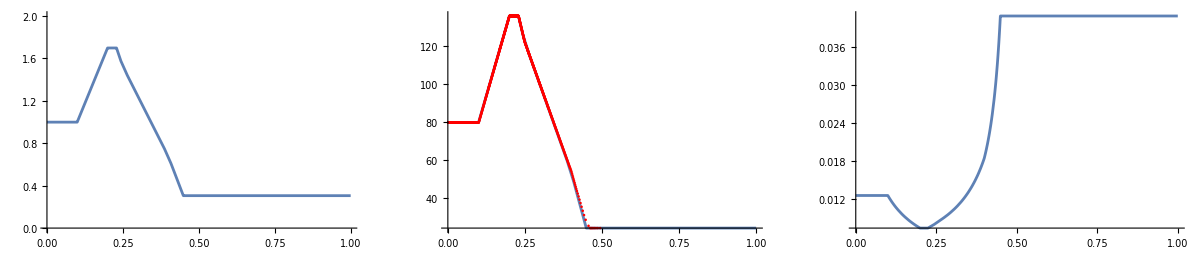

```mathematica
showRFunction[runCone]
```

### Disk map

```mathematica
diskTransform[{zMin_,zMax_}] := Module[{f},
f= Function[{xz},Module[{x,z,r},
{x,z}=xz;
r = zMax- z;
r= r/(zMax-zMin); (* outer ring radius 1 *)
r*{Cos[2 π x],Sin [ 2 π x]} 
]
];
f
];
```

```mathematica
makeDiskGraphics[run_] :=Module[{(*runDiskTransform,namedPolygons,namedType,namedPoints,colouredNodes,cropDisk,colouredPolygons,namedDiskNodes*)},
runDiskTransform := diskTransform[{stemParameters["ray"]["zStart"],stemParameters["inner"]["zEnd"]}];
namedDiskNodes = runTransformedNodes[run,runDiskTransform] ;
namedPolygons = namedPointsToVoronoiPolygons[namedDiskNodes];

namedType = nodeType /@  runTransformedNodes[run,Identity];
namedPoints = Point /@ runTransformedNodes[run,runDiskTransform];
colouredNodes= Association@Map[#->{nodeColour[namedType[#]],PointSize[Small],namedPoints[#]}&,Keys[namedPoints]];

cropDisk = {FaceForm[White],EdgeForm[White],MeshPrimitives[DiscretizeRegion[RegionDifference[Rectangle[1.2*{-1,-1},1.2*{1,1}],Disk[{0,0},1.02]]],2]};colouredPolygons =Map[{polygonColour[namedType[#]],EdgeForm[polygonBoundaryColour[namedType[#]]],namedPolygons[#]}&,
Keys@namedPolygons];

seedRun=DiskStacking`pruneRun[run,{stemParameters["seed"]["zStart"],stemParameters["seed"]["zEnd"]}];

seedParastichyLeft = Select[graphToContactLines[seedRun,leftRightColours],First[#]==leftRightColours[[1]]&];
seedDiskParastichy = seedParastichyLeft /. Line[line_]:> Line[Map[runDiskTransform,line]];
lColour = leftRightColours[[1]];
seedDiskParastichy = seedDiskParastichy /. lColour:>Directive[Opacity[0.5],leftRightColours[[1]]];

plotRange=1.02
*{{-1,1},{-1,1}};
diskShow  = Graphics[{
colouredPolygons
,seedDiskParastichy
,Values[colouredNodes]
,cropDisk
},
PlotRange->plotRange
]
];



runTransformedNodes[run_,transform_,bareOnly_:False] := Module[{g,nodeNames,namedNodes,namedDiskNodes},
g=run["ContactGraph"];
If[bareOnly,
nodeNames = diskNumbersInRun[run],
nodeNames = VertexList[g]
];

namedNodes = Association@Map[#->AnnotationValue[{g,#},VertexCoordinates]&,nodeNames];
namedNodes= Select[namedNodes,#=!= $Failed&];
namedDiskNodes = transform /@ namedNodes;
namedDiskNodes
];

namedPointsToVoronoiPolygons[namedPoints_] := Module[{voronoi,vPolygons,polygonToPoint},
voronoi= VoronoiMesh[Values[namedPoints]];
vPolygons = MeshPrimitives[voronoi,2];
polygonToPoint[polygon_] := Module[{f,node},
f=RegionMember[polygon];
node= First@Keys@Select[namedPoints,f];
node -> polygon
];
Association@Map[polygonToPoint,Take[vPolygons,All]]
];

namedPointsPeriodicToVoronoiPolygons[namedNodes_] := Module[{},
overlap=0.2;
leftNodes = KeyMap[left,Select[namedNodes,#[[1]]<=-0.5+overlap&]];
leftNodes = Map[#+{1,0}&,leftNodes];
rightNodes =  KeyMap[right,Select[namedNodes,#[[1]]>= 0.5 -overlap&]];
rightNodes = Map[#-{1,0}&,rightNodes];
vPoint = Join[namedNodes,leftNodes,rightNodes];
vPoly =namedPointsToVoronoiPolygons[vPoint];
nvPoly= KeySelect[vPoly,NumberQ];
nvPoly
];
```

### Cylinder

```mathematica
makeCylinderGraphics[run_] := Module[{},
namedPoints = Point /@ runTransformedNodes[run,Identity,bareOnly=True];
namedType = nodeType /@  runTransformedNodes[run,Identity];
colouredNodes= Association@Map[#->{cylinderNodeColour[namedType[#]],PointSize[Small],namedPoints[#]}&,Keys[namedPoints]];
namedDisks = runDisks[run];
colouredDisks= Association@Map[#->{
FaceForm[cylinderDiskColour[namedType[#]]]
,EdgeForm[cylinderDiskBoundaryColour[namedType[#]]]
,namedDisks[#]}&,Keys[namedDisks]];
textOffset[type_] := If[type==="bract",{-1,.75},{-1,0}];
partLabels =<|"cone"->"Uncommitted","bract"->"Bracts","ray"->"Ray florets","seed"-> "Seeds","inner"->"Unset seeds"|>;
partText =Style[KeyValueMap[Text[partLabels[#1],{0.55,Mean[{#2["zStart"],#2["zEnd"]}]},textOffset[#1]]&,stemParameters],jFont[12]];
cropRectangle = {FaceForm[White],EdgeForm[None],Rectangle[{1/2,-1},{2,10}]};
seedRun=DiskStacking`pruneRun[run,{stemParameters["seed"]["zStart"],stemParameters["seed"]["zEnd"]}];
seedParastichyLeft = Select[graphToContactLines[seedRun,leftRightColours],First[#]==leftRightColours[[1]]&];

Graphics[{Values@colouredDisks,seedParastichyLeft,cropRectangle,partText},PlotRange->{{-1/2,.9},{stemParameters["cone"]["zStart"],stemParameters["inner"]["zEnd"]}}]
];
```

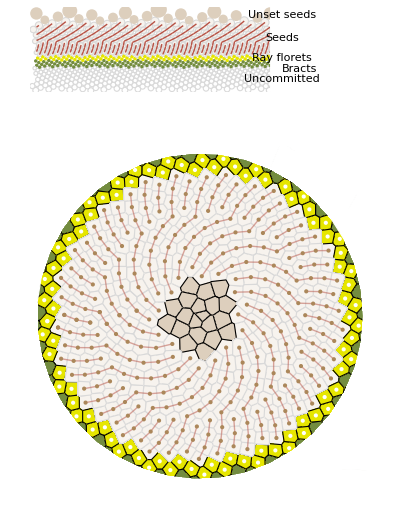

```mathematica
maketlkConeTransformation :=Module[{},
runCone= getRunByTag["radius-34bis-tlk3"]["Run"];
stemParameters = runCone["Arena"]["rFunctionList"] ;
stemParameters = KeyMap[<|1->"cone",2->"bract",3->"ray",4->"seed",5->"inner"|>[#]&,stemParameters];
diskRun = DiskStacking`pruneRun[runCone,{stemParameters["bract"]["zStart"],stemParameters["inner"]["zEnd"]}];
diskShow :=makeDiskGraphics[diskRun];
cylinderRun = DiskStacking`pruneRun[runCone,{stemParameters["cone"]["zStart"],stemParameters["inner"]["zEnd"]}];
cylinderShow = makeCylinderGraphics[cylinderRun];
 GraphicsColumn[{cylinderShow,diskShow},Frame->False]
];
tlkConeTransformation=maketlkConeTransformation
jExport[tlkConeTransformation]
```

### Stem map

```mathematica
polygonTransform[p_Polygon,transform_]:= Module[{listTransform},
listTransform[x_] := Map[transform,x];
Polygon[listTransform /@ (List@@p)]
];
```

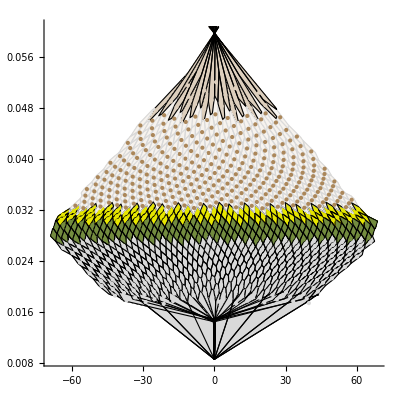

```mathematica
makeStemGraphics[run_] := Module[{},
rzData = Transpose[{Values@runDisksHeight[run,bareOnly=True],Values@runDisksRadius[run,bareOnly=True]}];
rzFunction = Interpolation[rzData];
Off[InterpolatingFunction::dmval];

zFlatten[z_] := Module[{},
If[z<stemParameters["ray"]["rEnd"],Return[z]];
stemParameters["ray"]["rEnd"]+ (z - stemParameters["ray"]["rEnd"])/10
];

rzTransform  = Function[{xz},Module[{x,z,rScale},
{x,z}=xz;
rScale = rzFunction[z];
x = x/rScale;
{x,zFlatten[z]}
]
];
namedType = nodeType /@  runDisksDivergenceHeight[run,True];

cylinderNodes =  runDisksDivergenceHeight[run,True];
namedNodes = rzTransform /@ runDisksDivergenceHeight[run,True];
colouredNodes= Association@Map[#->{cylinderNodeColour[namedType[#]],PointSize[Small],Point[namedNodes[#]]}&,Keys[namedNodes]];

cylinderPolygons = namedPointsPeriodicToVoronoiPolygons[cylinderNodes];
stemPolygons = Map[polygonTransform[#,rzTransform]&,cylinderPolygons];
colouredPolygons =Map[{polygonColour[namedType[#]],EdgeForm[polygonBoundaryColour[namedType[#]]],stemPolygons[#]}&,
Keys@stemPolygons];
 

Graphics[{colouredPolygons,Values@colouredNodes}(*,PlotRange ->{{-70,70},{0,1}}*), AspectRatio->1,Axes->True]
];
makeStemGraphics[cylinderRun]
```

```mathematica
makeStemGraphics3DPolygons[run_] := Module[{},
rzData = Transpose[{Values@runDisksHeight[run,bareOnly=True],Values@runDisksRadius[run,bareOnly=True]}];
minimumRadius = Min[Last/@rzData];
rzData = Map[{#[[1]],#[[2]]/minimumRadius}&,rzData];

rzFunction = Interpolation[rzData];
Off[InterpolatingFunction::dmval];

zFlatten[z_] := Module[{},
If[z<stemParameters["ray"]["zEnd"],Return[z]];
stemParameters["ray"]["zEnd"]+ (z - stemParameters["ray"]["zEnd"])/10
];


rz3Transform =  Function[{xz},Module[{x,z,stemRadius,theta},
{x,z}= xz;
stemRadius = 1/rzFunction[z];
theta = x * 2 π;
{stemRadius * Cos[theta],stemRadius*Sin[theta],zFlatten[z]}
]
];

namedType = nodeType /@  runDisksDivergenceHeight[run,True];

cylinderNodes =  runDisksDivergenceHeight[run,True];
namedNodes = rz3Transform /@ runDisksDivergenceHeight[run,True];
colouredNodes3D= Association@Map[#->{cylinderNodeColour[namedType[#]],PointSize[Small],Point[namedNodes[#]]}&,Keys[namedNodes]];

cylinderPolygons = namedPointsPeriodicToVoronoiPolygons[cylinderNodes];
stemPolygons = Map[polygonTransform[#,rz3Transform]&,cylinderPolygons];
colouredPolygons3D =Map[{polygonColour3D[namedType[#]],EdgeForm[polygonBoundaryColour[namedType[#]]],stemPolygons[#]}&,
Keys@stemPolygons];
  colouredPolygons3D =Association@Map[#->{polygonColour3D[namedType[#]],EdgeForm[polygonBoundaryColour[namedType[#]]],stemPolygons[#]}&,
Keys@stemPolygons];
<|"Voronoi"->colouredPolygons3D,"Nodes"->colouredNodes3D|>
 ];

makeStemGraphics3D[voronoiNodes_,nodeMax_:∞] := Module[{},
voronoi= Values@KeySelect[voronoiNodes["Voronoi"],#<= nodeMax&];
nodes= Values@KeySelect[voronoiNodes["Nodes"],#<= nodeMax&];
Graphics3D[{voronoi,nodes},PlotRange->{{-1,1},{-1,1},{0.13,0.268}},BoxRatios->{1,1,1.5},ViewPoint->{0,-20,10},
Lighting->"Neutral",
Boxed->False,Axes->False,SphericalRegion->True]
];
```

```mathematica
polynodes = makeStemGraphics3DPolygons[cylinderRun];
polynodes[[1]]//Keys // MinMax
```

{159,1029}

```mathematica
makeStemGraphics3D[polynodes,1029]
```

-Graphics3D-

```mathematica
(*av2 = AnimationVideo[makeStemGraphics3D[polynodes,n],{n,400,1029,1},RasterSize->300,DefaultDuration->30]*)
```

```mathematica
graphToContactLines[run_,leftRightColours_] := graphToContactLines[run["ContactGraph"],run,leftRightColours];

graphToContactLines[g_,run_,leftRightColours_] := Module[{dlines,fsort,res},
dlines = Line/@Map[diskXZ[getDiskFromRun[run,#]]&,List@@@EdgeList[g],{2}];fsort[Line[{p1_,p2_}]] := If[First[p1]<First[p2],Line[{p1,p2}],Line[{p2,p1}]];dlines=Map[fsort,dlines];res = lineCylinderIntersectionColoured[#,leftRightColours]& /@dlines;
res
];


lineCylinderIntersectionColoured[Line[{{x1_,z1_},{x2_,z2_}}],leftRightColours_] :=
 Module[{slope,col},
slope= (z2-z1)/(x2-x1);
If[slope>0,col=leftRightColours["Left"],col=leftRightColours["Right"]];If[x1<-1/2,Return[
{col,
Line[{{-1/2, z2 - slope * (x2-(-1/2))},{x2,z2}}], Line[{{x1+1,z1},{1/2,z1+slope *( 1/2-(1+x1))}}]
}
]];
If[x2>1/2,Return[
{col,
Line[{{-1/2, z2- slope * (x2-1-(-1/2))},{x2-1,z2}}], Line[{{x1,z1},{1/2,z1+slope *( 1/2-(x1))}}]
}
]];
Return[{col,Line[{{x1,z1},{x2,z2}}]}] 
];
```